# Physics 234 PS #4 (A)

## Ziyang Gao, 4/9/2018

The problem is about generate a random walk simulation in which the object has an equal chance of going either directions every time he chooses where to go, and he will be absorbed once he reaches in the positive direction, a or in the negative direction, b. The following code keeps track of the object’s route before he is absorbed at either point, with a maximum number steps of 100. We also use a=-2 and b=8 to check if our code works. There’s definitely space to improve the elegance and efficiency of our code, but I still haven’t find a way through Mathematica.

```mathematica
Clear[steps]
steps[n_]:=Table[2 RandomInteger[{0,1}]-1,{n}];
tValues[n_]:=Table[i,{i,0,n}];
```

```mathematica
data = steps[100]
tempResult = Rest[FoldList[If[#1+#2> -2 && #1+#2< 8 ,#1+#2,101]&,0,#]]&@data
result = Select[tempResult,#<90&]
len = Length[result]
Transpose[{tValues[len-1], result}]
```

{-1,1,1,1,-1,1,-1,-1,1,-1,1,-1,1,-1,1,-1,-1,-1,-1,-1,-1,-1,1,-1,-1,1,1,-1,-1,1,1,1,1,-1,-1,1,1,-1,-1,-1,-1,-1,1,1,1,-1,-1,1,1,-1,-1,-1,1,1,1,1,1,-1,1,-1,-1,1,-1,1,-1,-1,1,-1,1,1,-1,-1,1,1,-1,-1,1,-1,1,-1,-1,1,1,-1,-1,-1,1,-1,-1,1,1,-1,-1,-1,1,-1,-1,-1,-1,-1}

{-1,0,1,2,1,2,1,0,1,0,1,0,1,0,1,0,-1,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101}

{-1,0,1,2,1,2,1,0,1,0,1,0,1,0,1,0,-1}

17

(0 | -1
1 | 0
2 | 1
3 | 2
4 | 1
5 | 2
6 | 1
7 | 0
8 | 1
9 | 0
10 | 1
11 | 0
12 | 1
13 | 0
14 | 1
15 | 0
16 | -1)

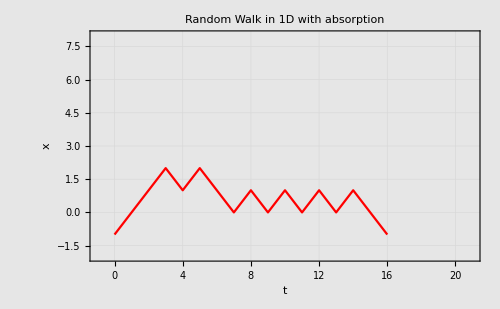

```mathematica
{xMin,xMax}={-2,8};
seed=123;SeedRandom[seed];
ListPlot[Transpose[{tValues[len-1], result}],PlotStyle->RGBColor[1,0,0],Frame->True,FrameLabel->{"t","x"},Joined->True,GridLines->Automatic,PlotLabel->"Random Walk in 1D with absorption",ImageSize->500,Background->GrayLevel[0.9],PlotRange->{{-1,n+1},{xMin,xMax}}]
```